```mathematica
aparam=1.42;
a1=aparam/2*{3,Sqrt[3]};
a2=aparam/2*{3,-Sqrt[3]};

b1=2*Pi/(3*aparam)*{1,Sqrt[3]};
b2=2*Pi/(3*aparam)*{1,-Sqrt[3]};

delta1=aparam/2*{1,Sqrt[3]};
delta2=aparam/2*{1,-Sqrt[3]};
delta3=aparam*{-1,0};

deltaprimo1=+a1;
deltaprimo2=-a1;
deltaprimo3=+a2;
deltaprimo4=-a2;
deltaprimo5=+a2-a1;
deltaprimo6=-a2+a1;

TNNlist={a2+delta1,-a2+delta1,-a1+delta2};

SumDeltaK[kx_,ky_]:=Exp[I*{kx,ky}.delta1]+Exp[I*{kx,ky}.delta2]+Exp[I*{kx,ky}.delta3];
SumDeltaKstar[kx_,ky_]:=Conjugate[SumDeltaK[kx,ky]];
SumDeltaPrimo[kx_,ky_]:=Exp[I*{kx,ky}.deltaprimo1]+Exp[I*{kx,ky}.deltaprimo2]+Exp[I*{kx,ky}.deltaprimo3]+Exp[I*{kx,ky}.deltaprimo4]+Exp[I*{kx,ky}.deltaprimo5]+Exp[I*{kx,ky}.deltaprimo6];
SumDeltaPrimoStar[kx_,ky_]:=Conjugate[SumDeltaPrimo[kx,ky]];

E2p = -0.36;
gamma0=-2.78;
s0=0.106;
gamma1=-0.12;
s1=0.001;
gamma2=-0.068;
s2=0.003;

(*Haa=Hbb e Saa=Sbb*)
Hmat[kx_,ky_]:={{E2p+gamma1*SumDeltaPrimo[kx,ky],gamma0*SumDeltaK[kx,ky]+gamma2*Sum[Exp[I*{kx,ky}.TNNlist[[i]]],{i,1,3}]},{gamma0*SumDeltaKstar[kx,ky]+gamma2*Sum[Exp[-I*{kx,ky}.TNNlist[[i]]],{i,1,3}],E2p+gamma1*SumDeltaPrimoStar[kx,ky]}};
Smat[kx_,ky_]:={{1+s1*SumDeltaPrimo[kx,ky],(s0*SumDeltaK[kx,ky]+s2*Sum[Exp[I*{kx,ky}.TNNlist[[i]]],{i,1,3}])},{(s0*SumDeltaKstar[kx,ky]+s2*Sum[Exp[-I*{kx,ky}.TNNlist[[i]]],{i,1,3}]),1+s1*SumDeltaPrimoStar[kx,ky]}};

Htotal[kx_,ky_,Ek_]:=Hmat[kx,ky]-Ek*Smat[kx,ky];
En/.Solve[Det[Htotal[1,1,En]]==0,En];
```

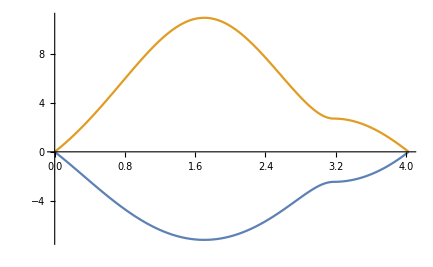

-Graphics3D-

```mathematica
Kcoord1=2 Pi/(3*aparam)*{1,1/Sqrt[3]};
Kcoord2=2 Pi/(3*aparam)*{1,-1/Sqrt[3]};
Mcoord=2 Pi/(3*aparam)*{1,0};

Kpath1=Table[Kcoord2-Kcoord2*i/100,{i,0,100}];
Kpath2=Table[Mcoord*i/60,{i,1,60}];
Kpath3=Table[Mcoord+(Kcoord2-Mcoord)*i/30,{i,1,30}];
Kpath=Catenate[{Kpath1,Kpath2,Kpath3}];

ValoriPlot2D=Transpose[Table[En/.Solve[Det[Htotal[Kpath[[i,1]],Kpath[[i,2]],En]]==0,En],{i,1,Length[Kpath]}]];

KpathDelta=Table[Norm[Kpath[[i]]-Kpath[[i-1]]],{i,1,Length[Kpath]}];
KpathDelta[[1]]=0;
KpathLength=Table[Sum[KpathDelta[[j]],{j,1,i}],{i,1,Length[Kpath]}];

Branch1=Table[{KpathLength[[i]],ValoriPlot2D[[1,i]]},{i,1,Length[Kpath]}];
Branch2=Table[{KpathLength[[i]],ValoriPlot2D[[2,i]]},{i,1,Length[Kpath]}];
ListPlot[{Branch1,Branch2},Joined->True,PlotRange->All]
Plot3D[{En/.Solve[Det[Htotal[kx,ky,En]]==0,En]}, {kx,-2,2},{ky,-2,2},PlotRange->{{-2,2},{-2,2},{-13,13}}]
```

{-16.7874,-10.4271,-6.76673,-4.4632,6.0421,8.07769,10.2328,18.8282}

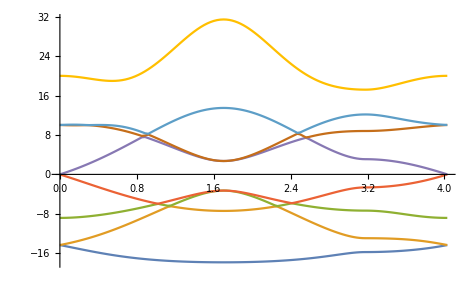

```mathematica
aparam=1.42;
delta1=aparam/2*{1,Sqrt[3]};
delta2=aparam/2*{1,-Sqrt[3]};
delta3=aparam*{-1,0};

deltadir1={delta1[[1]]/Norm[delta1],delta1[[2]]/Norm[delta1]};
deltadir2={delta2[[1]]/Norm[delta2],delta2[[2]]/Norm[delta2]};
deltadir3={delta3[[1]]/Norm[delta3],delta3[[2]]/Norm[delta3]};

(*Valori da predere dai paper*)
E2s=-8.868;
E2p=-0.36;


(*Presi da Dresselhaus*)
Hss=-6.769;
Hsp=5.580;
Hsig=5.037;
Hpi=-3.033;

Oss=0.212;
Osp=-0.102;
Osig=-0.146;
Opi=0.129;
(*Definisco i termini delle matrici uno ad uno così poi le matrici sono più pulite*)
Vss[kx_,ky_]:=Hss * SumDeltaK[kx,ky];

Vsx[kx_,ky_]:=deltadir1[[1]]*Hsp*Exp[I*{kx,ky}.delta1]+deltadir2[[1]]*Hsp*Exp[I*{kx,ky}.delta2]+deltadir3[[1]]*Hsp*Exp[I*{kx,ky}.delta3];

Vsy[kx_,ky_]:=deltadir1[[2]]*Hsp*Exp[I*{kx,ky}.delta1]+deltadir2[[2]]*Hsp*Exp[I*{kx,ky}.delta2];

Vxx[kx_,ky_]:=(((deltadir1[[1]]^2)*Hsig)+((1-(deltadir1[[1]]^2))*Hpi))*Exp[I*{kx,ky}.delta1]+(((deltadir2[[1]]^2)*Hsig)+((1-(deltadir2[[1]]^2))*Hpi))*Exp[I*{kx,ky}.delta2]+(((deltadir3[[1]]^2)*Hsig)+((1-(deltadir3[[1]]^2))*Hpi))*Exp[I*{kx,ky}.delta3];

Vyy[kx_,ky_]:=(((deltadir1[[2]]^2)*Hsig)+((1-(deltadir1[[2]]^2))*Hpi))*Exp[I*{kx,ky}.delta1]+(((deltadir2[[2]]^2)*Hsig)+((1-(deltadir2[[2]]^2))*Hpi))*Exp[I*{kx,ky}.delta2]+(((deltadir3[[2]]^2)*Hsig)+((1-(deltadir3[[2]]^2))*Hpi))*Exp[I*{kx,ky}.delta3];

Vxy[kx_,ky_]:=(((deltadir1[[1]])*(deltadir1[[2]])*Hsig)-((deltadir1[[1]])*(deltadir1[[2]])*Hpi))*Exp[I*{kx,ky}.delta1]+(((deltadir2[[1]])*(deltadir2[[2]])*Hsig)-((deltadir2[[1]])*(deltadir2[[2]])*Hpi))*Exp[I*{kx,ky}.delta2];

Vxs[kx_,ky_]:=deltadir1[[1]]*(-Hsp)*Exp[I*{kx,ky}.delta1]+deltadir2[[1]]*(-Hsp)*Exp[I*{kx,ky}.delta2]+deltadir3[[1]]*(-Hsp)*Exp[I*{kx,ky}.delta3];

Vys[kx_,ky_]:=deltadir1[[2]]*(-Hsp)*Exp[I*{kx,ky}.delta1]+deltadir2[[2]]*(-Hsp)*Exp[I*{kx,ky}.delta2];

Vyx[kx_,ky_]:=(((deltadir1[[1]])*(deltadir1[[2]])*(Hsig))-((deltadir1[[1]])*(deltadir1[[2]])*(Hpi)))*Exp[I*{kx,ky}.delta1]+(((deltadir2[[1]])*(deltadir2[[2]])*(Hsig))-((deltadir2[[1]])*(deltadir2[[2]])*(Hpi)))*Exp[I*{kx,ky}.delta2];

(*Coniugati*)
Vssstar[kx_,ky_]:=Hss * SumDeltaKstar[kx,ky];

Vsxstar[kx_,ky_]:=deltadir1[[1]]*(-Hsp)*Exp[-I*{kx,ky}.delta1]+deltadir2[[1]]*(-Hsp)*Exp[-I*{kx,ky}.delta2]+deltadir3[[1]]*(-Hsp)*Exp[-I*{kx,ky}.delta3];

Vsystar[kx_,ky_]:=deltadir1[[2]]*(-Hsp)*Exp[-I*{kx,ky}.delta1]+deltadir2[[2]]*(-Hsp)*Exp[-I*{kx,ky}.delta2];

Vxxstar[kx_,ky_]:=(((deltadir1[[1]]^2)*Hsig)+((1-(deltadir1[[1]]^2))*Hpi))*Exp[-I*{kx,ky}.delta1]+(((deltadir2[[1]]^2)*Hsig)+((1-(deltadir2[[1]]^2))*Hpi))*Exp[-I*{kx,ky}.delta2]+(((deltadir3[[1]]^2)*Hsig)+((1-(deltadir3[[1]]^2))*Hpi))*Exp[-I*{kx,ky}.delta3];

Vyystar[kx_,ky_]:=(((deltadir1[[2]]^2)*Hsig)+((1-(deltadir1[[2]]^2))*Hpi))*Exp[-I*{kx,ky}.delta1]+(((deltadir2[[2]]^2)*Hsig)+((1-(deltadir2[[2]]^2))*Hpi))*Exp[-I*{kx,ky}.delta2]+(((deltadir3[[2]]^2)*Hsig)+((1-(deltadir3[[2]]^2))*Hpi))*Exp[-I*{kx,ky}.delta3];

Vxystar[kx_,ky_]:=(((deltadir1[[1]])*(deltadir1[[2]])*(Hsig))-((deltadir1[[1]])*(deltadir1[[2]])*(Hpi)))*Exp[-I*{kx,ky}.delta1]+(((deltadir2[[1]])*(deltadir2[[2]])*(Hsig))-((deltadir2[[1]])*(deltadir2[[2]])*(Hpi)))*Exp[-I*{kx,ky}.delta2];

Vxsstar[kx_,ky_]:=deltadir1[[1]]*(Hsp)*Exp[-I*{kx,ky}.delta1]+deltadir2[[1]]*(Hsp)*Exp[-I*{kx,ky}.delta2]+deltadir3[[1]]*(Hsp)*Exp[-I*{kx,ky}.delta3];

Vysstar[kx_,ky_]:=deltadir1[[2]]*(Hsp)*Exp[-I*{kx,ky}.delta1]+deltadir2[[2]]*(Hsp)*Exp[-I*{kx,ky}.delta2];

Vyxstar[kx_,ky_]:=(((deltadir1[[1]])*(deltadir1[[2]])*(Hsig))-((deltadir1[[1]])*(deltadir1[[2]])*(Hpi)))*Exp[-I*{kx,ky}.delta1]+(((deltadir2[[1]])*(deltadir2[[2]])*(Hsig))-((deltadir2[[1]])*(deltadir2[[2]])*(Hpi)))*Exp[-I*{kx,ky}.delta2];


(*termini della matrice di overlap*)
Sss[kx_,ky_]:=Oss * SumDeltaK[kx,ky];

Ssx[kx_,ky_]:=deltadir1[[1]]*Osp*Exp[I*{kx,ky}.delta1]+deltadir2[[1]]*Osp*Exp[I*{kx,ky}.delta2]+deltadir3[[1]]*Osp*Exp[I*{kx,ky}.delta3];

Ssy[kx_,ky_]:=deltadir1[[2]]*Osp*Exp[I*{kx,ky}.delta1]+deltadir2[[2]]*Osp*Exp[I*{kx,ky}.delta2];

Sxx[kx_,ky_]:=(((deltadir1[[1]]^2)*Osig)+((1-(deltadir1[[1]]^2))*Opi))*Exp[I*{kx,ky}.delta1]+(((deltadir2[[1]]^2)*Osig)+((1-(deltadir2[[1]]^2))*Opi))*Exp[I*{kx,ky}.delta2]+(((deltadir3[[1]]^2)*Osig)+((1-(deltadir3[[1]]^2))*Opi))*Exp[I*{kx,ky}.delta3];

Syy[kx_,ky_]:=(((deltadir1[[2]]^2)*Osig)+((1-(deltadir1[[2]]^2))*Opi))*Exp[I*{kx,ky}.delta1]+(((deltadir2[[2]]^2)*Osig)+((1-(deltadir2[[2]]^2))*Opi))*Exp[I*{kx,ky}.delta2]+(((deltadir3[[2]]^2)*Osig)+((1-(deltadir3[[2]]^2))*Opi))*Exp[I*{kx,ky}.delta3];

Sxy[kx_,ky_]:=(((deltadir1[[1]])*(deltadir1[[2]])*Osig)-((deltadir1[[1]])*(deltadir1[[2]])*Opi))*Exp[I*{kx,ky}.delta1]+(((deltadir2[[1]])*(deltadir2[[2]])*Osig)-((deltadir2[[1]])*(deltadir2[[2]])*Opi))*Exp[I*{kx,ky}.delta2];

Sxs[kx_,ky_]:=deltadir1[[1]]*(-Osp)*Exp[I*{kx,ky}.delta1]+deltadir2[[1]]*(-Osp)*Exp[I*{kx,ky}.delta2]+deltadir3[[1]]*(-Osp)*Exp[I*{kx,ky}.delta3];

Sys[kx_,ky_]:=deltadir1[[2]]*(-Osp)*Exp[I*{kx,ky}.delta1]+deltadir2[[2]]*(-Osp)*Exp[I*{kx,ky}.delta2];

Syx[kx_,ky_]:=(((deltadir1[[1]])*(deltadir1[[2]])*(Osig))-((deltadir1[[1]])*(deltadir1[[2]])*(Opi)))*Exp[I*{kx,ky}.delta1]+(((deltadir2[[1]])*(deltadir2[[2]])*(Osig))-((deltadir2[[1]])*(deltadir2[[2]])*(Opi)))*Exp[I*{kx,ky}.delta2];

(*Coniugati*)
Sssstar[kx_,ky_]:=Oss * SumDeltaKstar[kx,ky];

Ssxstar[kx_,ky_]:=deltadir1[[1]]*(-Osp)*Exp[-I*{kx,ky}.delta1]+deltadir2[[1]]*(-Osp)*Exp[-I*{kx,ky}.delta2]+deltadir3[[1]]*(-Osp)*Exp[-I*{kx,ky}.delta3];

Ssystar[kx_,ky_]:=deltadir1[[2]]*(-Osp)*Exp[-I*{kx,ky}.delta1]+deltadir2[[2]]*(-Osp)*Exp[-I*{kx,ky}.delta2];

Sxxstar[kx_,ky_]:=(((deltadir1[[1]]^2)*Osig)+((1-(deltadir1[[1]]^2))*Opi))*Exp[-I*{kx,ky}.delta1]+(((deltadir2[[1]]^2)*Osig)+((1-(deltadir2[[1]]^2))*Opi))*Exp[-I*{kx,ky}.delta2]+(((deltadir3[[1]]^2)*Osig)+((1-(deltadir3[[1]]^2))*Opi))*Exp[-I*{kx,ky}.delta3];

Syystar[kx_,ky_]:=(((deltadir1[[2]]^2)*Osig)+((1-(deltadir1[[2]]^2))*Opi))*Exp[-I*{kx,ky}.delta1]+(((deltadir2[[2]]^2)*Osig)+((1-(deltadir2[[2]]^2))*Opi))*Exp[-I*{kx,ky}.delta2]+(((deltadir3[[2]]^2)*Osig)+((1-(deltadir3[[2]]^2))*Opi))*Exp[-I*{kx,ky}.delta3];

Sxystar[kx_,ky_]:=(((deltadir1[[1]])*(deltadir1[[2]])*(Osig))-((deltadir1[[1]])*(deltadir1[[2]])*(Opi)))*Exp[-I*{kx,ky}.delta1]+(((deltadir2[[1]])*(deltadir2[[2]])*(Osig))-((deltadir2[[1]])*(deltadir2[[2]])*(Opi)))*Exp[-I*{kx,ky}.delta2];

Sxsstar[kx_,ky_]:=deltadir1[[1]]*(Osp)*Exp[-I*{kx,ky}.delta1]+deltadir2[[1]]*(Osp)*Exp[-I*{kx,ky}.delta2]+deltadir3[[1]]*(Osp)*Exp[-I*{kx,ky}.delta3];

Sysstar[kx_,ky_]:=deltadir1[[2]]*(Osp)*Exp[-I*{kx,ky}.delta1]+deltadir2[[2]]*(Osp)*Exp[-I*{kx,ky}.delta2];

Syxstar[kx_,ky_]:=(((deltadir1[[1]])*(deltadir1[[2]])*(Osig))-((deltadir1[[1]])*(deltadir1[[2]])*(Opi)))*Exp[-I*{kx,ky}.delta1]+(((deltadir2[[1]])*(deltadir2[[2]])*(Osig))-((deltadir2[[1]])*(deltadir2[[2]])*(Opi)))*Exp[-I*{kx,ky}.delta2];

(*definizione delle due matrici*)
Hma[kx_,ky_]:={{E2p+gamma1*SumDeltaPrimo[kx,ky],Hpi*SumDeltaK[kx,ky]+gamma2*Sum[Exp[I*{kx,ky}.TNNlist[[i]]],{i,1,3}],0,0,0,0,0,0},

{Hpi*SumDeltaKstar[kx,ky]+gamma2*Sum[Exp[-I*{kx,ky}.TNNlist[[i]]],{i,1,3}],E2p+gamma1*SumDeltaPrimoStar[kx,ky],0,0,0,0,0,0},

{0,0,E2s,0,0,Vss[kx,ky],Vsx[kx,ky],Vsy[kx,ky]},

{0,0,0,E2p,0,Vxs[kx,ky],Vxx[kx,ky],Vxy[kx,ky]},

{0,0,0,0,E2p,Vys[kx,ky],Vyx[kx,ky],Vyy[kx,ky]},

{0,0,Vssstar[kx,ky],Vsxstar[kx,ky],Vsystar[kx,ky],E2s,0,0},

{0,0,Vxsstar[kx,ky],Vxxstar[kx,ky],Vxystar[kx,ky],0,E2p,0},

{0,0,Vysstar[kx,ky],Vyxstar[kx,ky],Vyystar[kx,ky],0,0,E2p}};


Sma[kx_,ky_]:={{1+s1*SumDeltaPrimo[kx,ky],(Opi*SumDeltaK[kx,ky]+s2*Sum[Exp[I*{kx,ky}.TNNlist[[i]]],{i,1,3}]),0,0,0,0,0,0},

{(Opi*SumDeltaKstar[kx,ky]+s2*Sum[Exp[-I*{kx,ky}.TNNlist[[i]]],{i,1,3}]),1+s1*SumDeltaPrimoStar[kx,ky],0,0,0,0,0,0},

{0,0,1,0,0,Sss[kx,ky],Ssx[kx,ky],Ssy[kx,ky]},

{0,0,0,1,0,Sxs[kx,ky],Sxx[kx,ky],Sxy[kx,ky]},

{0,0,0,0,1,Sys[kx,ky],Syx[kx,ky],Syy[kx,ky]},

{0,0,Sssstar[kx,ky],Ssxstar[kx,ky],Ssystar[kx,ky],1,0,0},

{0,0,Sxsstar[kx,ky],Sxxstar[kx,ky],Sxystar[kx,ky],0,1,0},

{0,0,Sysstar[kx,ky],Syxstar[kx,ky],Syystar[kx,ky],0,0,1}};



Htot[kx_,ky_,Ek_]:=Hma[kx,ky]-Ek*Sma[kx,ky];
(*esempio di autovalori calcolati con kx = 1 e ky = 0, per controllare che sia tutto corretto*)
En/.Solve[Det[Htot[1,0,En]]==0,En]

(*per fare il grafico*)
Kcoord1=2 Pi/(3*aparam)*{1,1/Sqrt[3]};
Kcoord2=2 Pi/(3*aparam)*{1,-1/Sqrt[3]};
Mcoord=2 Pi/(3*aparam)*{1,0};

Kpath1=Table[Kcoord2-Kcoord2*i/50,{i,0,50}];
Kpath2=Table[Mcoord*i/50,{i,0,50}];
Kpath3=Table[Mcoord+(Kcoord2-Mcoord)*i/50,{i,0,50}];
Kpath=Catenate[{Kpath1,Kpath2,Kpath3}];

ValoriPlot2D=Transpose[Table[En/.Solve[Det[Htot[Kpath[[i,1]],Kpath[[i,2]],En]]==0,En],{i,1,Length[Kpath]}]];

KpathDelta=Table[Norm[Kpath[[i]]-Kpath[[i-1]]],{i,1,Length[Kpath]}];
KpathDelta[[1]]=0;
KpathLength=Table[Sum[KpathDelta[[j]],{j,1,i}],{i,1,Length[Kpath]}];

Branch1=Table[{KpathLength[[i]],ValoriPlot2D[[1,i]]},{i,1,Length[Kpath]}];
Branch2=Table[{KpathLength[[i]],ValoriPlot2D[[2,i]]},{i,1,Length[Kpath]}];
Branch3=Table[{KpathLength[[i]],ValoriPlot2D[[3,i]]},{i,1,Length[Kpath]}];
Branch4=Table[{KpathLength[[i]],ValoriPlot2D[[4,i]]},{i,1,Length[Kpath]}];
Branch5=Table[{KpathLength[[i]],ValoriPlot2D[[5,i]]},{i,1,Length[Kpath]}];
Branch6=Table[{KpathLength[[i]],ValoriPlot2D[[6,i]]},{i,1,Length[Kpath]}];
Branch7=Table[{KpathLength[[i]],ValoriPlot2D[[7,i]]},{i,1,Length[Kpath]}];
Branch8=Table[{KpathLength[[i]],ValoriPlot2D[[8,i]]},{i,1,Length[Kpath]}];
ListPlot[{Branch1,Branch2,Branch3,Branch4,Branch5,Branch6,Branch7,Branch8},Joined->True,PlotRange->All]
```

601

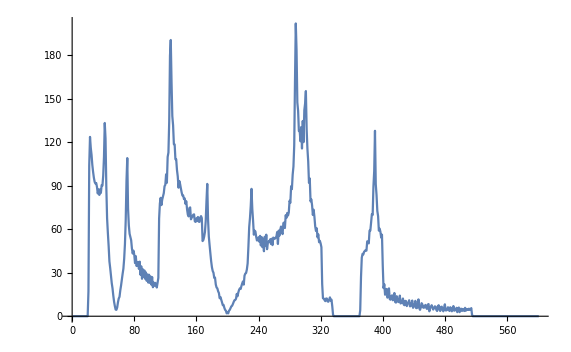

```mathematica
(*Calcoli per la DOS*)
Karea={};
listakx=Table[(i-1)/60,{i,61}];
listaky=Table[(-1/Sqrt[3])*((i-1)/60),{i,61}];
soglia=(Kcoord2[[2]])/(Kcoord2[[1]]);
For[i=1,i≤ 61,i++,For[j=1,j≤ 61,j++,If[listaky[[j]]≥(listakx[[i]]*soglia),AppendTo[Karea,{listakx[[i]],listaky[[j]]}]]]];
Length[Karea];

Karea = Karea*Kcoord1[[1]];
Epos = Table[i, {i,-20, 40, 0.1}];
DOS = Table[0, {i,-20, 40, 0.1}];
Etable =Table[En/.Solve[Det[Htot[Karea[[i]][[1]], Karea[[i]][[2]],En]]==0, En],{i,1,Length[Karea]}];
For[i=1,i ≤Length[Etable], i++,(For[j=1, j≤8, j++,
DOS[[Round[((Etable[[i,j]]+20)/0.1)-1]]]+=0.2;
DOS[[Round[(Etable[[i,j]]+20)/0.1]]]+=1;
DOS[[Round[((Etable[[i,j]]+20)/0.1)+1]]]+=0.2;
])];
Length[DOS]
ListPlot[DOS, Joined -> True]
```